## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW170104";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
samples["dalpha_3"][[6]]
```

## m1-m2 Plot, 22

## INSPIRAL

### phi_2

```mathematica
(* ==========================================*)
(*1. 数据提取与概率密度 (不变)*)
(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];m2Data=samples[p][[2]];
devData=samples[p][[5]];
grData=samples[p][[6]];   (*GR 系数值*)
paramData=samples[p][[7]];  (*GR*(1+d) 参数化值*)

m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{16,33},{1,7}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

contourPD[p]={0.001};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",True][[1]][[2]];
```

输入Mc范围：{16,33}

输入q范围：{1,7}

m1范围：{18.3792,108.936}

m2范围：{7.54535,37.907}

对称数据：原始 21307 + 镜像 21307

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.995821（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{7.54535, 108.936} × {7.54535, 108.936}

等高线值：{0.001}，共 2 条

第一条前3点：{{29.7932,30.11},{29.7484,30.1655},{29.7067,30.2171}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.832673

可信水平百分比：83.2673%

==========================

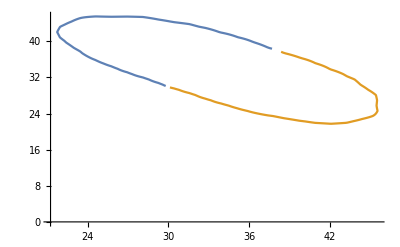

```mathematica
ListLinePlot[contourPoints[p]]
```

0.831126

0.5

dphi_2 grTargets = {6.22281,6.35214}

dphi_2 paramTargets = {5.83737,6.50536}

dphi_2 GR 线有效点数：下=8 上=13

dphi_2 参数化线有效点数：下=1 上=24

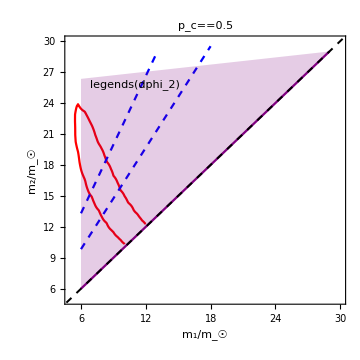

```mathematica
probability=prob
probability=0.5

(* ==========================================*)(*2. 解析参数名+计算目标值*)(* ==========================================*)
m1s=Range[5,30,1];m2s=Range[5,30,1];

pInterval=IntervalFromProbability[probability/2];

tapeIntervals["mass1"]=Quantile[m1Data,pInterval];
tapeIntervals["mass2"]=Quantile[m2Data,pInterval];

(*⭐ 解析参数名：自动拼出真实的物理函数*)
paramCore=StringDrop[p,1];  (*"dphi_2"->"phi_2"*)
{typeName,orderStr}=StringSplit[paramCore,"_"];
orderVal=If[StringEndsQ[orderStr,"l"],orderStr,ToExpression[orderStr]];
realFuncName=Symbol["IMRPhenomD"<>Capitalize[typeName]<>"NS"];

(*⭐⭐⭐ 关键修复：强制 N[] 确保目标值一定是数字 ⭐⭐⭐*)
grTargets=N[Quantile[N[grData],N[pInterval]]];     (*两个数字：{下界,上界}*)
paramTargets=N[Quantile[N[paramData],N[pInterval]]]; (*两个数字：{下界,上界}*)

(*打印验证*)
Print[p," grTargets = ",grTargets];
Print[p," paramTargets = ",paramTargets];


(* ==========================================*)
(*3. 反解（GR 和参数化用同一个公式，目标值不同）*)
(* ==========================================*)
(*物理含义：GR 线：IMRPhenomDPhiNS[2,m1,m2,0,0]==GR系数的分位数 参数化线：IMRPhenomDPhiNS[2,m1,m2,0,0]==参数化值的分位数 两者用的是同一个解析函数，区别只在目标值*)
theFormula=Function[{h,m2,c1,c2},realFuncName[orderVal,h,m2,c1,c2]];

chi1Fixed=0;chi2Fixed=0;
fixedArgs={chi1Fixed,chi2Fixed};
h0guess=N[Median[m1Data]];
h0s={h0guess,h0guess}; (*两个目标值需要两个初始猜测*)

Quiet[grSurface=HypersurfacePancake[theFormula,grTargets,{m2s},{1},fixedArgs,h0s,1];
paramSurface=HypersurfacePancake[theFormula,paramTargets,{m2s},{1},fixedArgs,h0s,1];];


(* ==========================================*)
(*4. 裁剪（GR 两条线+参数化两条线）*)
(* ==========================================*)
(*通用提取函数*)
extractLine[surface_,idx_]:=If[MatchQ[surface,{__List}]&&Length[surface]>=idx&&Length[surface[[idx]]]>1,Select[surface[[idx]][[2;;]],Function[pt,m2s[[1]]<=pt[[2]]<=m2s[[-1]]]],{}];

(*GR：下界线+上界线*)
grLineDown=extractLine[grSurface,1];
grLineUp=extractLine[grSurface,2];

(*参数化：下界线+上界线*)
lineDown=extractLine[paramSurface,1];
lineUp=extractLine[paramSurface,2];

Print[p," GR 线有效点数：下=",Length[grLineDown]," 上=",Length[grLineUp]];
Print[p," 参数化线有效点数：下=",Length[lineDown]," 上=",Length[lineUp]];


(* ==========================================*)(*6. 绘图（有啥画啥，哪怕只有一条边）*)(* ==========================================*)(*---动态组装线条---*)linesToPlot={};
plotStyles={};

(*红色：概率密度等值线（始终画）*)
AppendTo[linesToPlot,contourPoints[p][[1]]];
AppendTo[plotStyles,Red];

(*蓝色虚线：GR 反解线（有就画）*)
If[Length[grLineDown]>0,AppendTo[linesToPlot,grLineDown];
AppendTo[plotStyles,Directive[Blue,Dashed]]];
If[Length[grLineUp]>0,AppendTo[linesToPlot,grLineUp];
AppendTo[plotStyles,Directive[Blue,Dashed]]];

(*紫色：参数化反解线（有就画，哪怕只有一条边）*)
If[Length[lineDown]>0,AppendTo[linesToPlot,lineDown];
AppendTo[plotStyles,Purple]];
If[Length[lineUp]>0,AppendTo[linesToPlot,lineUp];
AppendTo[plotStyles,Purple]];


(*---Epilog 组装（彻底修复语法错误）---*)
epilogParts={};

(*1. 参数化区域填充（上下界都在时才填充，样式和图形基元平级）*)
If[Length[lineUp]>0&&Length[lineDown]>0,AppendTo[epilogParts,Directive[Purple,Opacity[0.2]]];(*只有样式*)AppendTo[epilogParts,Polygon[Flatten[{lineUp,Reverse[lineDown]},1]]]; (*图形基元*)];

(*2. 画参数化边界线*)
If[Length[lineDown]>0,AppendTo[epilogParts,Directive[Purple,Thickness[0.004]]];
AppendTo[epilogParts,Line[lineDown]];];
If[Length[lineUp]>0,AppendTo[epilogParts,Directive[Purple,Thickness[0.004]]];
AppendTo[epilogParts,Line[lineUp]];];

(*3. 图例和对角线（固定部分）*)
AppendTo[epilogParts,Directive[Black,Opacity[1]]];
AppendTo[epilogParts,Inset[legends[p],Scaled[{0.25,0.82}],{0,0}]];
AppendTo[epilogParts,Directive[Black,Dashed,Opacity[1]]];
AppendTo[epilogParts,Line[{{0,0},{100,100}}]];


(*---出图判断---*)
(*红色等值线+至少一条反解线 就画*)
If[Length[linesToPlot]>=2,ListLinePlot[linesToPlot,PlotStyle->plotStyles,Axes->False,Frame->True,FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},FrameStyle->Directive[Black,Thickness[0.004]],BaseStyle->{FontSize->15},AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},Epilog->epilogParts,PlotLabel->With[{value=probability},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],ImageSize->Medium],(*一条反解线都没有时*)Print["提示：",p," 没有任何反解线，跳过绘图。"]]
```

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0001};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 21307 + 镜像 21307

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 2.59131×10^-6 for the integral and error estimates.

对称先验空间积分 = 0.999999（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.59131×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.0001}，共 2 条

第一条前3点：{{40.6018,39.6006},{40.6043,39.6025},{40.6241,39.5907}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.966734

可信水平百分比：96.6734%

==========================

dphi_2 预处理完成，红线包含概率 prob = 0.966734

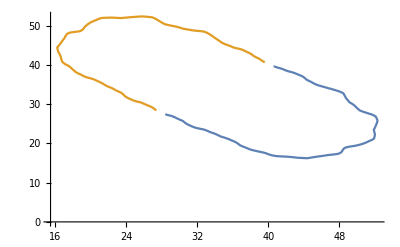

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

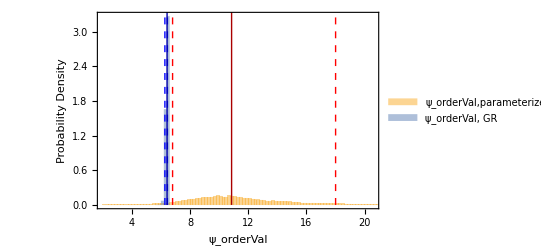

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0379, 0.9621}

实际使用的 GR 概率区间上下界: {6.25285, 6.44167}

实际使用的 Param 概率区间上下界: {6.44388, 18.7246}

GR下界: 点数=99 | 平均误差=2.15316×10^-16

GR上界: 点数=99 | 平均误差=7.35663×10^-16

Param下界: 点数=99 | 平均误差=0.00207763

Param上界: 点数=99 | 平均误差=12.2828

chi1L取值：0.459326

chi2L取值：0.4582

=====================================================

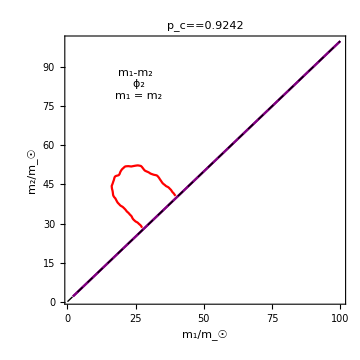

```mathematica
probability=prob;
probability=0.9242;

PlotInversion[p,probability,1,100,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.001};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20224 + 镜像 20224

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.55872×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.55872×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.001}，共 2 条

第一条前3点：{{37.7649,38.7666},{37.54,39.0091},{37.4765,39.09}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.823539

可信水平百分比：82.3539%

==========================

dphi_4 预处理完成，红线包含概率 prob = 0.823539

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

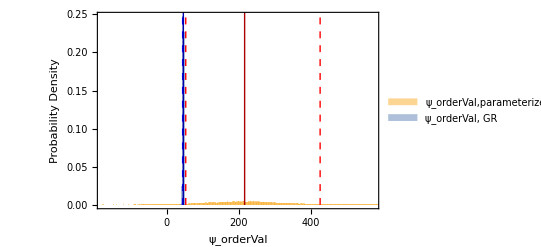

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.04385, 0.95615}

实际使用的 GR 概率区间上下界: {43.8577, 46.244}

实际使用的 Param 概率区间上下界: {46.3231, 438.915}

GR下界: 点数=197 | 平均误差=4.11177×10^-15

GR上界: 点数=197 | 平均误差=1.36338×10^-14

Param下界: 点数=197 | 平均误差=0.0772173

Param上界: 点数=197 | 平均误差=392.67

chi1L取值：0.509548

chi2L取值：0.467782

=====================================================

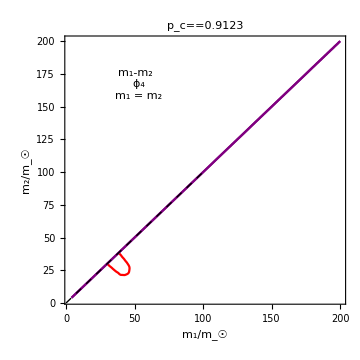

```mathematica
probability=prob;
probability=0.9123;

PlotInversion[p,probability,3,200,1,cm->True,cd->False,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_5l"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.001};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 17541 + 镜像 17541

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.12838×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.12838×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.001}，共 2 条

第一条前3点：{{37.7513,38.753},{37.5081,39.0111},{37.4557,39.0692}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.82634

可信水平百分比：82.634%

==========================

dphi_5l 预处理完成，红线包含概率 prob = 0.82634

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

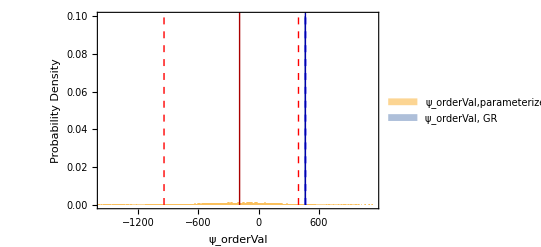

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.03425, 0.96575}

实际使用的 GR 概率区间上下界: {464.758, 466.978}

实际使用的 Param 概率区间上下界: {-1048., 463.799}

GR下界: 点数=485 | 平均误差=6.17659×10^-14

GR上界: 点数=485 | 平均误差=3.03556×10^-14

Param下界: 点数=485 | 平均误差=1512.76

Param上界: 点数=485 | 平均误差=0.957668

chi1L取值：0.418848

chi2L取值：0.455312

=====================================================

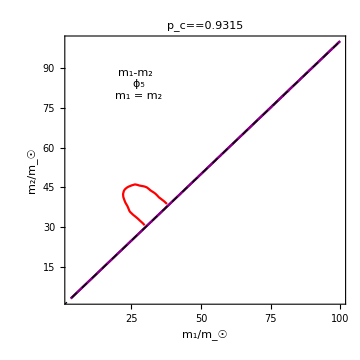

```mathematica
probability=prob;
probability=0.9315;

PlotInversion[p,probability,3,100,0.2,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiLNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.001};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 18248 + 镜像 18248

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.0438×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.0438×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.001}，共 2 条

第一条前3点：{{37.804,38.8057},{37.5901,39.0058},{37.491,39.1045}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.814809

可信水平百分比：81.4809%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.814809

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

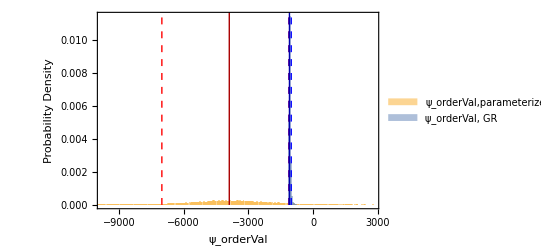

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.04915, 0.95085}

实际使用的 GR 概率区间上下界: {-1103.97, -1006.56}

实际使用的 Param 概率区间上下界: {-7033.68, -1102.5}

GR下界: 点数=970 | 平均误差=1.41347×10^-13

GR上界: 点数=970 | 平均误差=1.3408×10^-13

Param下界: 点数=970 | 平均误差=5929.55

Param上界: 点数=970 | 平均误差=1.45332×10^-13

chi1L取值：0.510796

chi2L取值：0.446253

=====================================================

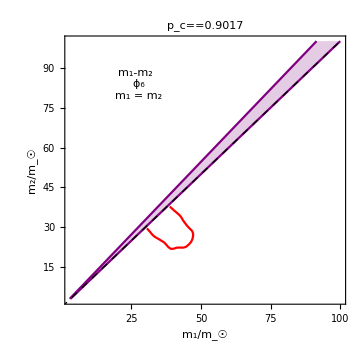

```mathematica
probability=prob;
probability=0.9016;

PlotInversion[p,probability,3,100,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_7"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0005376};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 17264 + 镜像 17264

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 6.11271×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 6.11271×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.0005376}，共 2 条

第一条前3点：{{29.6834,29.0208},{29.684,29.02},{29.705,28.9973}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.905821

可信水平百分比：90.5821%

==========================

dphi_7 预处理完成，红线包含概率 prob = 0.905821

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

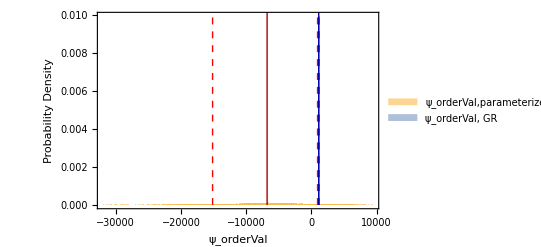

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0470894, 0.952911}

实际使用的 GR 概率区间上下界: {1112.67, 1130.87}

实际使用的 Param 概率区间上下界: {-15336., 1109.79}

GR下界: 点数=97 | 平均误差=1.17203×10^-14

GR上界: 点数=97 | 平均误差=4.21931×10^-14

Param下界: 点数=97 | 平均误差=16289.7

Param上界: 点数=97 | 平均误差=9.37623×10^-14

chi1L取值：0.479016

chi2L取值：0.448311

=====================================================

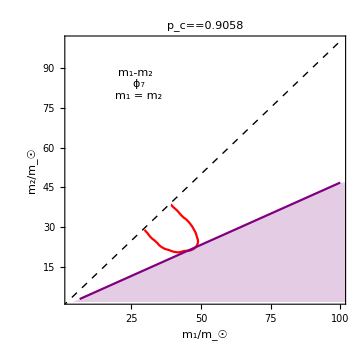

```mathematica
probability=prob;
(*probability=0.9045;*)
(*0.32*)
PlotInversion[p,probability,3,100,1,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1}]
```

## Intermediate

### beta_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00196};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20031 + 镜像 20031

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.3066×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.3066×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.00196}，共 2 条

第一条前3点：{{31.0992,32.099},{31.0959,32.0976},{30.9728,32.2108}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.54637

可信水平百分比：54.637%

==========================

dbeta_2 预处理完成，红线包含概率 prob = 0.54637

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

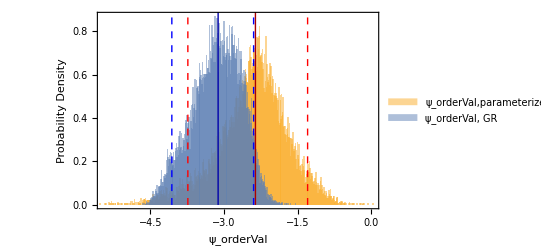

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dbeta_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.226815, 0.773185}

实际使用的 GR 概率区间上下界: {-3.5362, -2.73957}

实际使用的 Param 概率区间上下界: {-2.86884, -1.91766}

GR下界: 点数=50 | 平均误差=0.22367

GR上界: 点数=50 | 平均误差=1.01252×10^-15

Param下界: 点数=50 | 平均误差=1.1724×10^-15

Param上界: 点数=50 | 平均误差=8.26006×10^-16

chi1L取值：0.519556

chi2L取值：0.510708

=====================================================

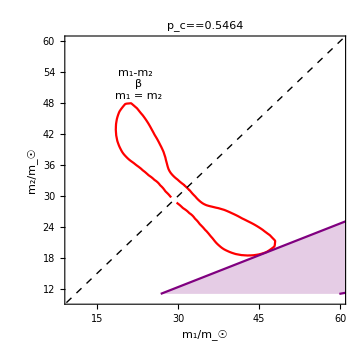

```mathematica
probability=prob;
(*probability=0.401;*)

PlotInversion[p,probability,10,60,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### beta_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.002};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20730 + 镜像 20730

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.48502×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 1.48502×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.002}，共 2 条

第一条前3点：{{31.4412,32.4429},{31.3496,32.5379},{31.1421,32.7557}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

警告：第 1 个区域点数不足，跳过积分

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.

可信水平百分比：0.%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

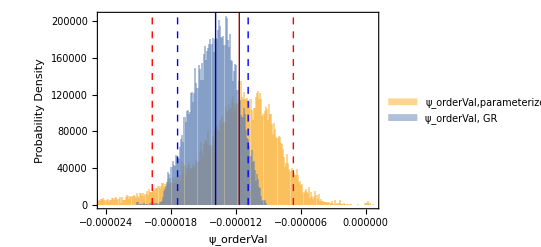

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.485, 0.515}

实际使用的 GR 概率区间上下界: {-0.0000139569, -0.0000137876}

实际使用的 Param 概率区间上下界: {-0.0000118214, -0.0000115536}

GR下界: 点数=50 | 平均误差=1.52922×10^-9

GR上界: 点数=50 | 平均误差=1.28749×10^-21

Param下界: 点数=50 | 平均误差=1.82852×10^-6

Param上界: 点数=50 | 平均误差=2.09633×10^-6

chi1L取值：0.44779

chi2L取值：0.449006

=====================================================

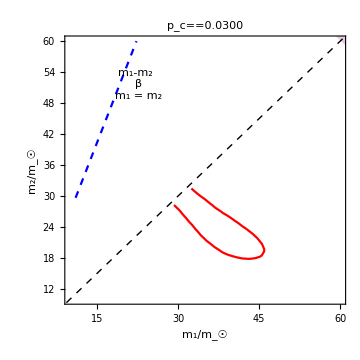

```mathematica
probability=prob;
probability=0.05;

(* 蓝色要对称一下 *)
PlotInversion[p,probability,10,60,1,cm->True,cd->False,cu->True,plotgr->True,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

# Merger-RingDown

### alpha_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.003666};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 22575 + 镜像 22575

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.49369×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.49369×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.003666}，共 2 条

第一条前3点：{{39.1327,20.8458},{39.4952,20.731},{39.5411,20.7164}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.230665

可信水平百分比：23.0665%

==========================

dalpha_2 预处理完成，红线包含概率 prob = 0.230665

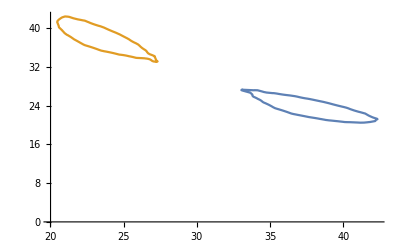

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

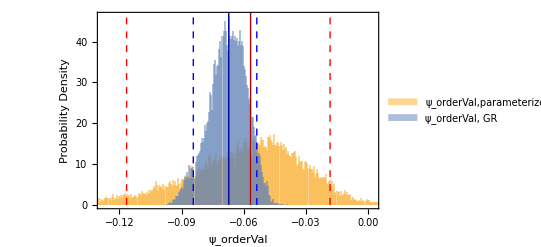

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.384668, 0.615332}

实际使用的 GR 概率区间上下界: {-0.0699701, -0.0644364}

实际使用的 Param 概率区间上下界: {-0.0651733, -0.0487595}

GR下界: 点数=40 | 平均误差=2.91434×10^-17

GR上界: 点数=40 | 平均误差=2.32453×10^-17

Param下界: 点数=40 | 平均误差=2.5327×10^-17

Param上界: 点数=40 | 平均误差=1.85615×10^-17

chi1L取值：0.411525

chi2L取值：0.493505

=====================================================

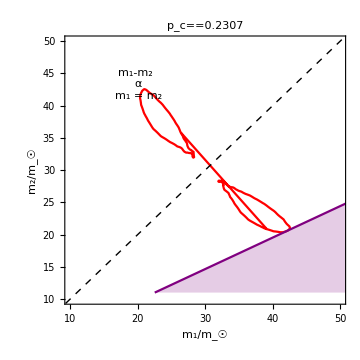

```mathematica
probability=prob;
(*probability=0.2;*)

PlotInversion[p,probability,10,50,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### alpha_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00396};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.103197

可信水平百分比：10.3197%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.103197

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 19232 + 镜像 19232

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.4036×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.4036×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.00396}，共 2 条

第一条前3点：{{34.9971,25.2895},{34.9617,25.2805},{34.715,25.2421}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.105445

可信水平百分比：10.5445%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.105445

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

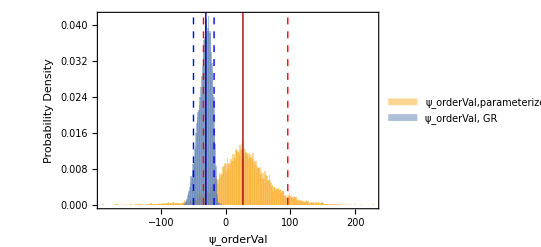

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.447277, 0.552723}

实际使用的 GR 概率区间上下界: {-22.7808, -20.3513}

实际使用的 Param 概率区间上下界: {-19.677, -9.35681}

GR下界: 点数=40 | 平均误差=2.80664×10^-14

GR上界: 点数=40 | 平均误差=2.54019×10^-14

Param下界: 点数=40 | 平均误差=3.32179×10^-14

Param上界: 点数=40 | 平均误差=3.09086×10^-14

chi1L取值：0.403505

chi2L取值：0.474398

=====================================================

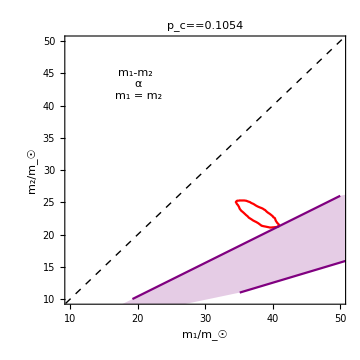

```mathematica
probability=prob;
(*probability=0.9999;*)

PlotInversion[p,probability,10,50,1,cm->True,cd->False,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1}]
```

### alpha_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.002};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 20196 + 镜像 20196

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.45029×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.45029×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.002}，共 2 条

第一条前3点：{{31.1992,32.2009},{30.9576,32.4464},{30.8633,32.5636}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

警告：合并后点数不足，无法构成多边形，跳过

Part::partd: Part specification ⟦2⟧ is longer than depth of object.

dalpha_4 预处理完成，红线包含概率 prob = ⟦2⟧

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

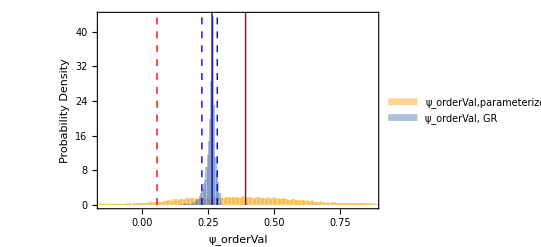

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
probability=prob;
probability=0.3905;

PlotInversion[p,probability,10,50,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.30475, 0.69525}

实际使用的 GR 概率区间上下界: {0.255744, 0.268392}

实际使用的 Param 概率区间上下界: {0.270707, 0.521802}

GR下界: 点数=40 | 平均误差=5.82867×10^-17

GR上界: 点数=40 | 平均误差=5.13478×10^-17

Param下界: 点数=40 | 平均误差=5.82867×10^-17

Param上界: 点数=40 | 平均误差=0.000127176

chi1L取值：0.475705

chi2L取值：0.4964

=====================================================

-Graphics-

# utils